# Homework 30

## Problem 30.1

Consider a pancake undergoing free rotation with no external torque. Its principal moments are 0.4, 0.4, and 0.7 kg m^2. Its initial angular velocity vector is (1, 0, 5) rad/s in the body frame. Let’s calculate how the pancake behaves.

```mathematica
Quit[]
```

First, a qualitative prediction: Will the angular velocity vector remain constant in this zero-torque situation?
Write your answer here (feel free to come back later and modify it): No

Now let’s calculate the behavior and see if your answer is correct. Let:
omega0 be the initial angular velocity vector
MI be the moment of inertia tensor (written just as a 3-component vector because all the off-diagonal elements are zero)
w1[t], w2[t], w3[t] be the components of the angular velocity as expressed in body coordinates

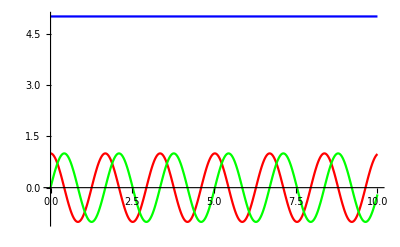

```mathematica
omega0={1,0,5};
MI={0.4,0.4,0.7};
eq1=MI[[1]]*w1'[t]==(MI[[2]]-MI[[3]])*w2[t]*w3[t];
eq2=MI[[2]]*w2'[t]==(MI[[3]]-MI[[1]])*w1[t]*w3[t];
eq3=MI[[3]]*w3'[t]==(MI[[1]]-MI[[2]])*w1[t]*w2[t];
bc={w1[0]==omega0[[1]],w2[0]==omega0[[2]],w3[0]==omega0[[3]]};
sol1=NDSolve[{eq1,eq2,eq3,bc[[1]],bc[[2]],bc[[3]]},{w1[t],w2[t],w3[t]},{t,0,10}];
Plot[{w1[t]/.sol1,w2[t]/.sol1,w3[t]/.sol1},{t,0,10},PlotStyle->{Red,Green,Blue}]
```

You should see that one of components of the angular velocity is constant while the other two vary sinusoidally. Briefly explain what this plot means physically for the angular velocity and angular momentum of the disk as observed in the body frame.

Type your answer here (a couple of sentences should be fine):

The angular velocity varies in the w1 and w2 directions and so has a variable angular momentum. The angular velocity in the w3
direction, however, is constant and so has zero angular momentum and its angular momentum is conserved.
Now let’s compare the numerical solution with the analytical solution given in Eq. 10.94.

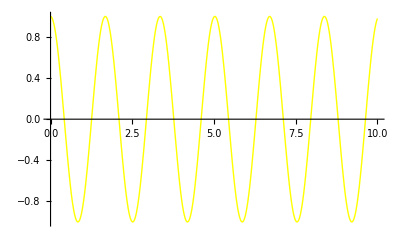

```mathematica
Omegab=(MI[[1]]-MI[[3]])/MI[[1]] w3[t];
Plot[{w1[t]/.sol1,omega0[[1]]*Cos[Omegab*t]},{t,0,10},PlotStyle->{{Yellow,Thick},{Blue,Dashed}}]
```

The two curves should agree.

They agree, the blue one is underneath the yellow one.

## Written Problems

-Graphics-